{{0.,6.},{0.1,5.90982},{0.2,5.8384},{0.3,5.78413},{0.4,5.74499},{0.5,5.71853},{0.6,5.70187},{0.7,5.69172},{0.8,5.68434},{0.9,5.67557},{1.,5.66081},{1.1,5.63505},{1.2,5.59281},{1.3,5.52821},{1.4,5.4349},{1.5,5.3061},{1.6,5.13457},{1.7,4.91259},{1.8,4.63196},{1.9,4.28397},{2.,3.85938},{2.1,3.34837},{2.2,2.74049},{2.3,2.02465},{2.4,1.189},{2.5,0.220937},{2.6,-0.893072},{2.7,-2.16752},{2.8,-3.61798},{2.9,-5.26127},{3.,-7.11556}}

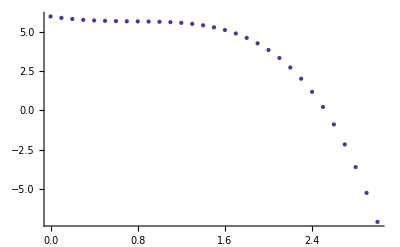

10.-1. ⅇ^x-3. Cos[x]

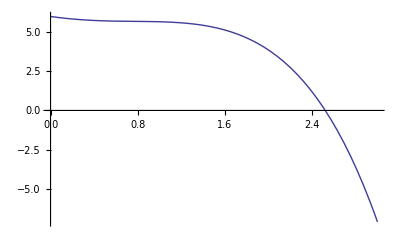

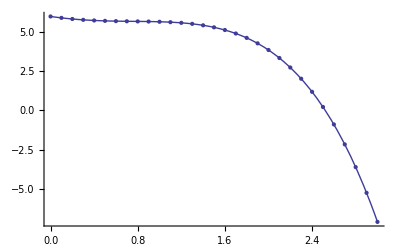

```mathematica
data=Table[{x,10-3Cos[x]- Exp[x]},{x,0,3,0.1}]
lp=ListPlot[data]
fit=Fit[data,{1,Cos[x],Exp[x]},x]
pl=Plot[fit,{x,0,3}]
Show[lp,pl]
```

{{0.,10.},{0.1,10.1003},{0.2,10.2027},{0.3,10.3093},{0.4,10.4228},{0.5,10.5463},{0.6,10.6841},{0.7,10.8423},{0.8,11.0296},{0.9,11.2602},{1.,11.5574},{1.1,11.9648},{1.2,12.5722},{1.3,13.6021},{1.4,15.7979},{1.5,24.1014}}

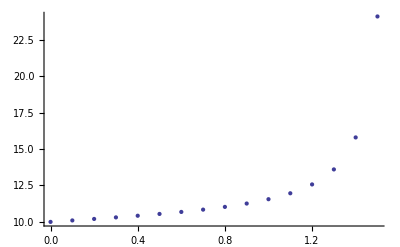

10.+2.35837×10^-16 ⅇ^(x^2)+1. Tan[x]

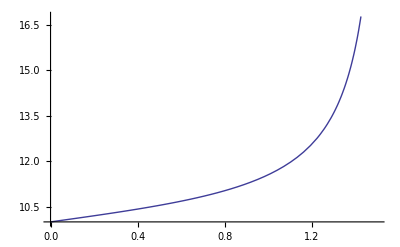

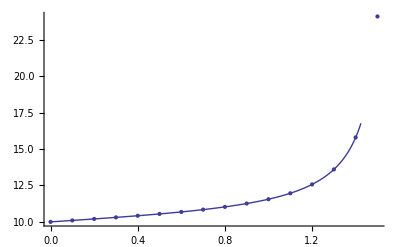

```mathematica
data=Table[{x,10+Tan[x]},{x,0,1.5,0.1}]
lp=ListPlot[data]
fit=Fit[data,{1,Tan[x], Exp[x x]},x]
pl=Plot[fit,{x,0,1.5}]
Show[lp,pl]
```